```mathematica
f[x_]=Sqrt[x^2+3x+1]
```

√(1+3 x+x^2)

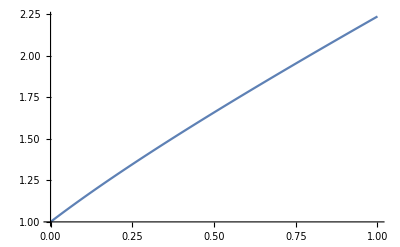

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
IfIwantedtomakeanestimate,maybeIwouldconsideritastraightline?IshouldbecarefulthoughbecausewheretheaxismeetisNOTTHEORIGIN!!!!I see a square that is 1 by 1 with a triangle on top so my guess at the area is
```

```mathematica
N[1*1+1/2*1*(f[1]-1)]
```

1.61803

The actual value is

```mathematica
NIntegrate[f[x],{x,0,1}]
```

1.64576

Not a bad guess!  Why did I subtract 1 from f[1]?

What if I want multiple graphs on the same axis?

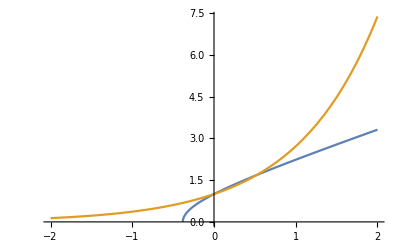

```mathematica
Plot[{f[x],E^x},{x,-2,2}]
```

```mathematica
I can zoom in and get a better idea of where they meet...
```

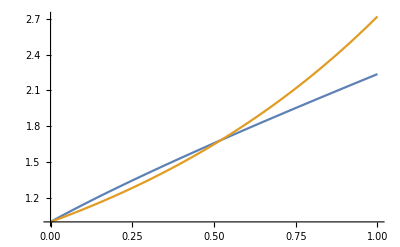

```mathematica
Plot[{f[x],E^x},{x,0,1}]
```

I find them with FindRoot

```mathematica
FindRoot[f[x]-E^x,{x,0}]
```

{x→0.}

That one was obvious...  Lets try for the other.

```mathematica
FindRoot[f[x]-E^x,{x,1}]
```

{x→0.520729}

```mathematica
I tried one there but I should have tried a much closer value...
```

Here I will make a picture of the rotation.  Your job is to find the volume.  (There was a formula we learned in class...

```mathematica
Show[RevolutionPlot3D[{f[x]},{x,0,.520729}],
RevolutionPlot3D[{E^x},{x,0,.520729}]]
```

-Graphics3D-

```mathematica
Number 3 is me trying to be clever and get you to make a proof.  Just do what it asks.  For a challenge, write out a complete proof of this identity (LinguisticAssistant
```

This last thing is for fun!  It is revolving x^2 around the x-axis.  With Manipulate you can make your own fun graphics.

```mathematica
theta0=Pi;
Manipulate[Row[{Plot[x^2,{x,0,1},PlotStyle->{Thick,Black},Filling->Axis,BaselinePosition->Axis,ImageSize->Small],RevolutionPlot3D[x^2,{x,0,1},{t,theta0-.001,T},PlotRange->{{0,1},{-1,1},{-1,1}},BoxRatios->1,Boxed->False,Axes->False,Mesh->None,RevolutionAxis->"X",PerformanceGoal->"Quality",BaselinePosition->Center,ImageSize->Small]}],{T,theta0,theta0+2 Pi}]
```